# Transmission coefficient as a function of the barrier width

```mathematica
T=1/(1+Subscript[V, 0]^2/(4 Ener (Subscript[V, 0]-Ener))Sinh[√((2 m(Subscript[V, 0]-Ener))/ℏ^2) a]^2);
```

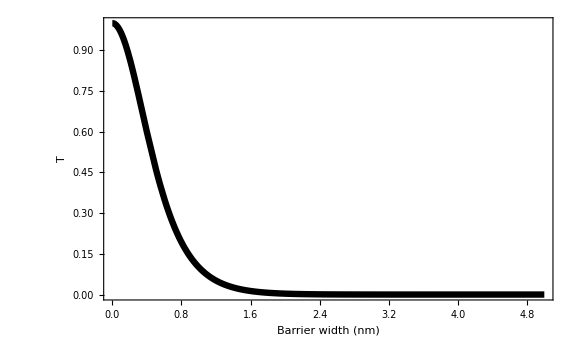

```mathematica
Plot[{T/.{Subscript[V, 0]->10,ℏ->1,Ener->7,m->0.5}},{a,0,5},
Frame->True,
FrameLabel->{"Barrier width (nm)","T"},FrameStyle->Black,PlotRange->{{0,5},{0,1}},Exclusions->None,PlotStyle->{Thickness@0.008,Black},LabelStyle->Directive[Black,25],ImageSize->Large]
```